```mathematica
Plot
```

Plot

```mathematica
Plot[Sin[x]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[Sin[x]]

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

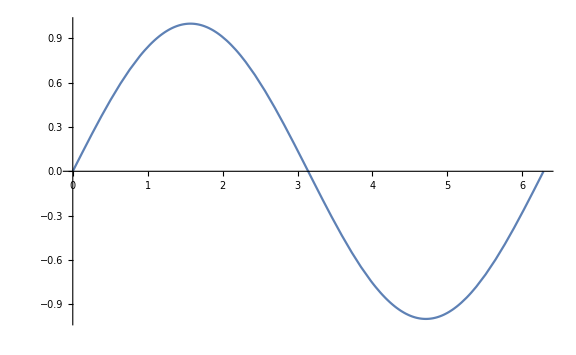

```mathematica
Plot[Sin[x],{x,0,2Pi},ImageSize->Large]
```

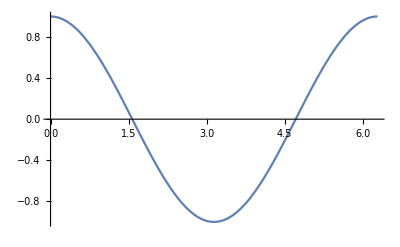

```mathematica
Plot[Cos[k],{k,0,2Pi}]
```

```mathematica
Exp[10]
```

ⅇ^10

```mathematica
e
```

e

```mathematica
N[E]
```

2.71828

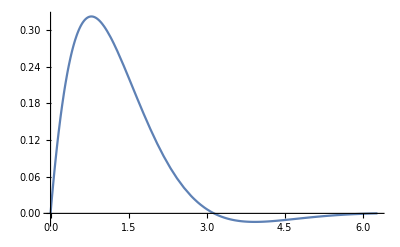

```mathematica
Plot[Exp[-x]Sin[x],{x,0,2Pi}]
```

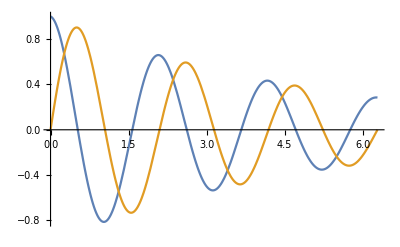

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi}]
```

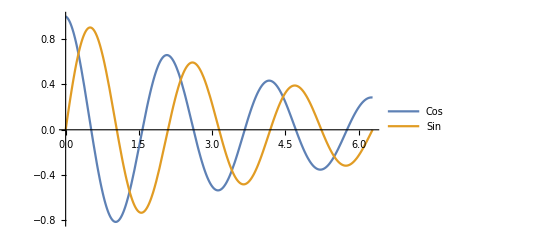

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi},PlotLegends->{"Cos","Sin"}]
```

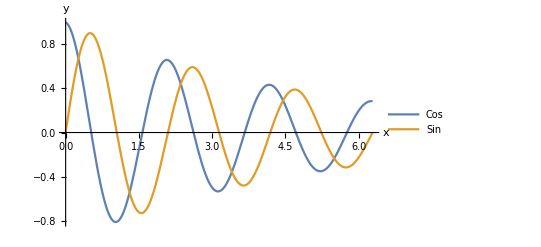

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi},PlotLegends->{"Cos","Sin"},AxesLabel->{"x","y"}]
```

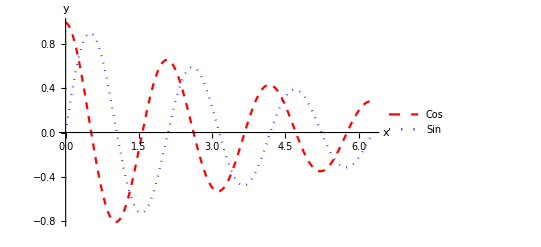

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi},PlotLegends->{"Cos","Sin"},AxesLabel->{"x","y"},PlotStyle->{{Red,Dashed,Thick},{Blue,Dotted}}]
```

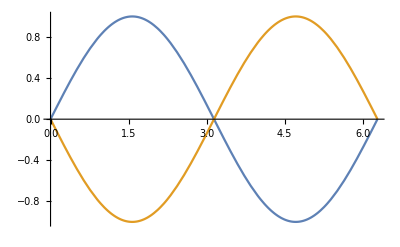

```mathematica
Plot[{Sin[x],Sin[x+Pi]},{x,0,2Pi}]
```

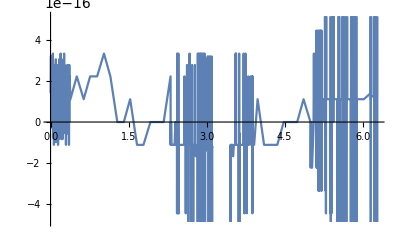

```mathematica
Plot[Sin[x]+Sin[x+Pi],{x,0,2Pi}]
```

```mathematica
?GraphicsRow
```

GraphicsRow[{g_1,g_2,…}] generates a graphic in which the g_i are laid out in a row.
GraphicsRow[list,spacing] leaves the specified spacing between successive elements.

```mathematica
GraphicsRow[{Plot[{Sin[x],Sin[x+Pi]},{x,0,2Pi}],Plot[Sin[x]+Sin[x+Pi],{x,0,2Pi}]}]
```

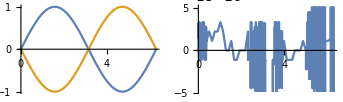

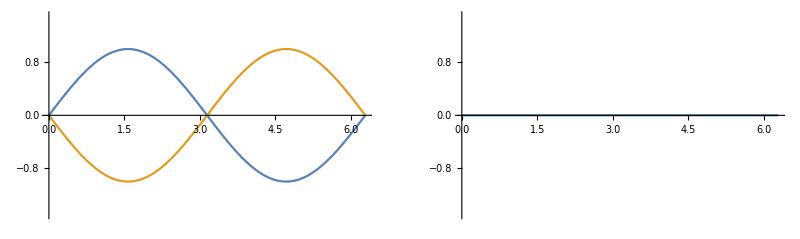

```mathematica
GraphicsRow[{
Plot[{Sin[x],Sin[x+Pi]},{x,0,2Pi},PlotRange->{Automatic,{-1.5,1.5}}],
Plot[Sin[x]+Sin[x+Pi],{x,0,2Pi},PlotRange->{Automatic,{-1.5,1.5}}]
}]
```